```mathematica
S[N_]:=k N (5/2+Log[(2 √2 π^(3/2) (k m T)^(3/2) V)/(h^3 N)])
```

```mathematica
Solve[(2 √2 π^(3/2) (k m T)^(3/2) V)/(h^3 N)==1,N]
```

{{N→(2 √2 k m π^(3/2) T √(k m T) V)/h^3}}

```mathematica
Solve[1/D[S[N],En]==T,En]
```

{{En→(3 k N T)/2}}

```mathematica
p V/T==D[S[N],V] V
```

(p V)/T==k N

```mathematica
Expand[ S'[N]]
```

k Log[(8 ((En m)/N)^(3/2) π^(3/2) V)/(3 √3 h^3 N)]

```mathematica
-(3 k T)/2
```

```mathematica
Simplify[k T Log[(2^(3/N) ((En m)/N)^(3/(2 N)) (π/3)^(3/(2 N)) V)/(h^3 N)]]
```

k T Log[(8^(1/N) ((En m)/N)^(3/(2 N)) (π/3)^(3/(2 N)) V)/(h^3 N)]

```mathematica
Simplify[k Log[(8 ((En m)/N)^(3/2) π^(3/2) V)/(3 √3 h^3 N)]-S[N]/N]
```

-(5 k)/2

```mathematica
Exit[]
```

```mathematica
DSolve[{F'[N]==F[N]/N+k T /2,F[N0]==F0},F[N],N]
```

{{F[N]→(2 F0 N+k N N0 T Log[N]-k N N0 T Log[N0])/(2 N0)}}

```mathematica
Simplify[(2 F0 N+k N N0 T Log[N]-k N N0 T Log[N0])/(2 N0)]
```

(N (2 F0+k N0 T Log[N]-k N0 T Log[N0]))/(2 N0)

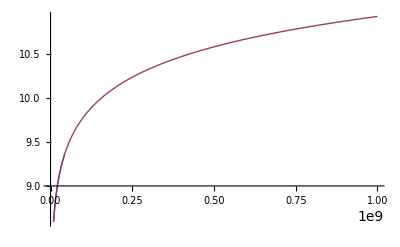

```mathematica
Plot[{Log[2^(2N)/(2N)!*N!*N!],0.5Log[Pi N]},{N,0,1000000000}]
```

```mathematica
Animate[Plot[(n^2)!/(n^2-x)!/x!/2^(n^2),{x,0,n^2},PlotRange->All],{n,1,10}]
```

```mathematica
0.4!
```

0.887264

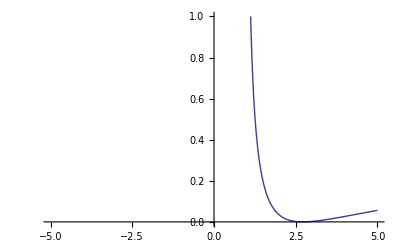

```mathematica
T=10^90;Plot[Log[1/4 (1/Log[x]+Log[x]+2)],{x,-5,5},PlotRange->{0,1}]
```

```mathematica
Animate[Plot[{c^2/3/4/V,(c^2/3+2)/4/V,c^5/V^5/2,(c+1)^5/V^5/2},{V,0,7},PlotRange->{0,0.7}],{c,0,5}]
```

```mathematica
,
```

```mathematica
,
```